# Reta x Elipse

### Reta

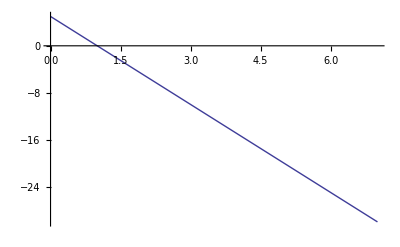

```mathematica
yreta=-5x+5;
retaPlot=Plot[yreta,{x,0,7}]
```

### Elipse

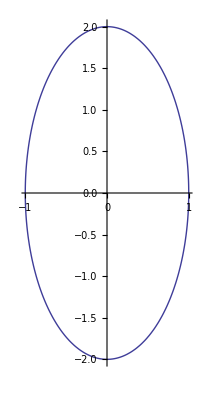

```mathematica
elipsePlot=ParametricPlot[{Cos[θ],2Sin[θ]},{θ,0,2π}]
```

### Intersecção

{{x→21/29},{x→1}}

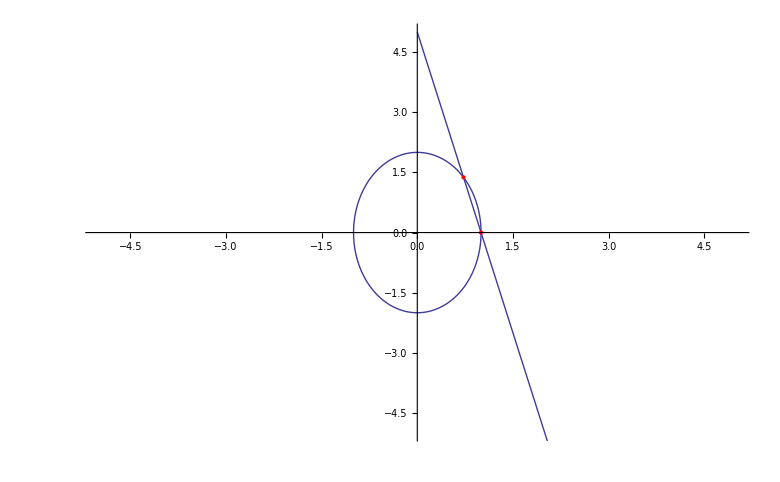

```mathematica
result=Solve[x^2+yreta^2/4==1,x]
pt1=Graphics[{Red,PointSize[Large],Point[{result[[1,1,2]],(yreta/.x->result[[1,1,2]])}]},Axes->True];
pt2=Graphics[{Red,PointSize[Large],Point[{result[[2,1,2]],(yreta/.x->result[[2,1,2]])}]}];
Show[retaPlot,elipsePlot,pt1,pt2,PlotRange->{{-5,5},{-5,5}}]
```

### Menor Distancia

```mathematica
ArcTan[{1,2}]
```

{π/4,ArcTan[2]}

```mathematica
MinimizePointElipseDistance[a_,b_,ponto_]:=Block[{xc,yc,tangent,normalellips,normalponto,ϕellips,ϕponto,FuncObj,dFuncObj,ϕn,ϕ,xn,ObjPlot},
yc=b Sin[ϕ];
xc=a Cos[ϕ];
tangent=D[{xc,yc},ϕ];

normalellips={tangent[[2]],-tangent[[1]]};
normalponto=ponto-{xc,yc};
ϕellips=ArcTan[normalellips[[1]],normalellips[[2]]];
ϕponto=ArcTan[normalponto[[1]],normalponto[[2]]];
FuncObj=ϕellips-ϕponto;
dFuncObj=D[FuncObj,ϕ];
Print["FuncObj = ",FuncObj];
ϕn=N[ArcTan[ponto[[1]],ponto[[2]]]];
For[angulo=0.,angulo<Pi/2.,angulo+=Pi/50.,If[(FuncObj/.ϕ->angulo)(FuncObj/.ϕ->angulo+Pi/50)<0,ϕn=angulo]];
Print["ϕn = ",ϕn];
ObjPlot=Plot[FuncObj/.ϕ->xe,{xe,0,Pi/2},PlotRange->All]; (* plotando o grafico*)

(* Tentei primeiro usar o mathematica mas nao deu
min=FindRoot[FuncObj,{xe,0}];
*)

(* Depois fiz o meu metodo de newton, mas nada *)
For[i=1,i≤5,i++,
Print["FuncObj = ",FuncObj/.ϕ->ϕn];
Print["dFuncObj = ",dFuncObj/.ϕ->ϕn];
ϕn=ϕn-(FuncObj/.ϕ->ϕn)/(dFuncObj/.ϕ->ϕn);
Print["ϕn = ",ϕn];
];
ObjPlot (*dai soh plotei a funcao*)
]
```

FuncObj = -ArcTan[150-100 Cos[ϕ],8-2 Sin[ϕ]]+ArcTan[2 Cos[ϕ],100 Sin[ϕ]]

ϕn = 0.

FuncObj = -0.158655

dFuncObj = 50.039

ϕn = 0.00317063

FuncObj = -0.00130632

dFuncObj = 48.8147

ϕn = 0.00319739

FuncObj = -2.70552×10^-7

dFuncObj = 48.7944

ϕn = 0.0031974

FuncObj = -1.16573×10^-14

dFuncObj = 48.7944

ϕn = 0.0031974

FuncObj = 0.

dFuncObj = 48.7944

ϕn = 0.0031974

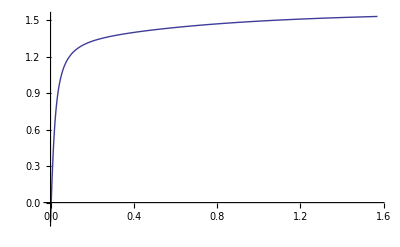

```mathematica
a=1;
b=2;
ponto={150,8};
MinimizePointElipseDistance[100,2,ponto]
```